Name: Karan Sharma
College Roll No.: 2232191
University Roll No.: 22036563079
Course: BSc. (Hons.) Mathematics/Year 3/Complex Analysis 
Section: A

## Practical 8. Plotting the given parametrized path.

Question 1: Find a parametrization of a line segment joining the two specified end points. Also plot the line segment

1.1 : z0 = -1 + ⅈ , z1 = 2 - ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -1 + ⅈ; z1 = 2 - ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

Set::write: Tag Plus in (x+ⅈ y)[t_] is Protected.

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -1+ⅈ and 2-ⅈ is

z[t] = (x+ⅈ y)[t] where 0 ≤ t ≤ 1

The required plot is

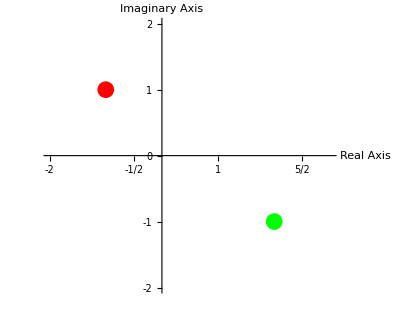

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

1.2 : z0 = -1 + 3 ⅈ,  z1 = 2 + ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -1 + 3 ⅈ; z1 = 2 + ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

Set::write: Tag Plus in (x+ⅈ y)[t_] is Protected.

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -1+3 ⅈ and 2+ⅈ is

z[t] = (x+ⅈ y)[t] where 0 ≤ t ≤ 1

The required plot is

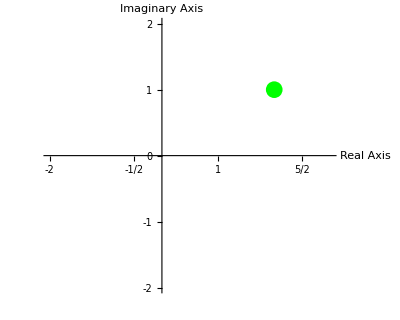

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

1.3 : z0 = -2 - ⅈ , z1 = 1 + ⅈ

```mathematica
(* Initial and Terminal points *) 
z0 = -2 - ⅈ; z1 = 1 + ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1];
```

```mathematica
Clear[z]
z[t_] = (x0 + (x1 - x0) t) + ⅈ (y0 + (y1 - y0) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}];
```

```mathematica
line = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, 1}, PlotRange -> {{-2, 3}, {-2, 2}}, 
Ticks -> {Range[-2, 3, 1 / 2], Range[-2, 2, 1 / 2]}, PlotStyle -> Blue, AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

Equation of the line segment joining the points -2-ⅈ and 1+ⅈ is

z[t] = -2+3 t+ⅈ (-1+2 t) where 0 ≤ t ≤ 1

The required plot is

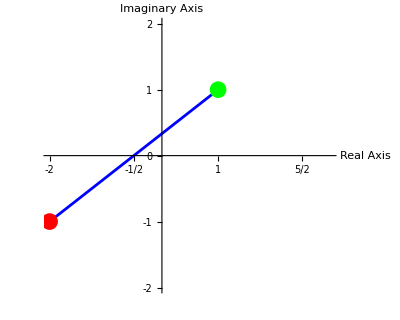

```mathematica
Print["Equation of the line segment joining the points ", z0, " and ", z1, " is "]; 
Print[" z[t] = ", z[t], " where 0 ≤ t ≤ 1"]; 
Print["The required plot is "]; 
Show[line, dot0, dot1]
```

Question 2: Find a parametrization of a polygonal path C. Also make a plot of it.

2.1 : C = C1 + C2 + C3 from - 1 + ⅈ to 3 - ⅈ 
	where  C1 is a line from - 1 + ⅈ to - 1, 
    		C2 is a line from - 1 to 1 + ⅈ, 
            		C3 is a line from 1 + ⅈ to 3 - ⅈ.

```mathematica
(* Initial and Terminal points of the paths Ci *) 
z0 = -1 + ⅈ; z1 = -1; z2 = 1 + ⅈ; z3 = 3 - ⅈ; 
(* Real and Imaginary parts of given points *) 
x0 = Re[z0]; 
y0 = Im[z0]; 
x1 = Re[z1]; 
y1 = Im[z1]; 
x2 = Re[z2]; 
y2 = Im[z2]; 
x3 = Re[z3];
y3 = Im[z3];
```

```mathematica
(* Equation of path C1: Line joining z0 to z1 *)
p1[t_] = (x0 + (x1 - x0) t) +ⅈ (y0 + (y1 - y0) t); 
(* Equation of path C2: Line joining z1 to z2 *) 
p2[t_] = (x1 + (x2 - x1) t) +ⅈ (y1 + (y2 - y1) t); 
(* Equation of path C3: Line joining z2 to z3 *) 
p3[t_] = (x2 + (x3 - x2) t) + ⅈ (y2 + (y3 - y2) t);
```

```mathematica
dot0 = Graphics[{PointSize[0.03], Red, Point[{Re[z0], Im[z0]}]}]; 
dot1 = Graphics[{PointSize[0.03], Green, Point[{Re[z1], Im[z1]}]}]; 
dot2 = Graphics[{PointSize[0.03], Blue, Point[{Re[z2], Im[z2]}]}]; 
dot3 = Graphics[{PointSize[0.03], Orange, Point[{Re[z3], Im[z3]}]}];
```

```mathematica
line = ParametricPlot[ {{Re[p1[t]], Im[p1[t]]}, 
{Re[p2[t]], Im[p2[t]]}, {Re[p3[t]], Im[p3[t]]}}, {t, 0, 1}, 
PlotRange -> {{-2, 4}, {-2, 2}}, PlotStyle -> {Purple},
AxesLabel -> {"Real Axis", "Imaginary Axis"}];
```

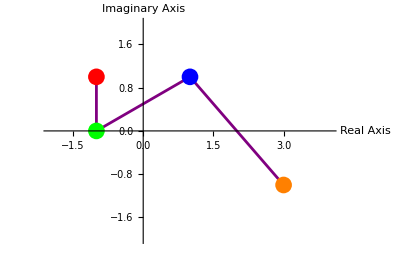

```mathematica
Show[line, dot0, dot1, dot2, dot3]
```

Question 3: Find a parametrization of the given curve. Also make a plot of it.

3.1 : C is the portion of the parabola x = y^2 + 2 y joining - 1 - ⅈ to 3 + ⅈ.

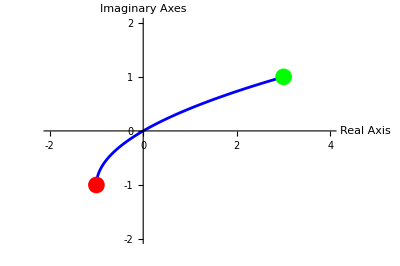

```mathematica
Clear[z]
z[t_] = (t^2 + 2 t) + ⅈ t; 
g1 = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, -1, 1}, 
PlotRange -> {{-2, 4}, {-2, 2}}, Ticks -> {Range[-2, 4, 1], 
Range[-2, 2, 1]}, AxesLabel -> {"Real Axis", "Imaginary Axes"},
PlotStyle -> Blue];

g2 = Graphics[{PointSize[0.03], Red, Point[{-1, -1}], Green, Point[{3, 1}]}]; 

Show[ g1, g2]
```

3.2 : C is the upper semicircle with radius 1 centered at point (2, 0) in the anticlockwise sense.

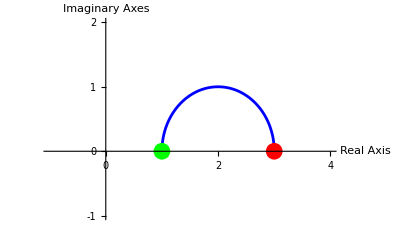

```mathematica
Clear[z]
z[t_] = (2 + Cos[t]) + ⅈ Sin[t]; 
g1 = ParametricPlot[{Re[z[t]], Im[z[t]]}, {t, 0, π}, 
PlotRange -> {{-1, 4}, {-1, 2}}, Ticks -> {Range[-2, 4, 1], Range[-2, 2, 1]}, 
AxesLabel -> {"Real Axis", "Imaginary Axes"}, PlotStyle -> Blue]; 
g2 = Graphics[{PointSize[0.03], Red, Point[{3, 0}], Green, Point[{1, 0}]}]; 
Show[ g1, g2]
```